Kaushik Chakram 
                                                                                                                     Professor Julia Kamenetzky
                                                                                                                     phys 425 &01
                                                                                                                     April, 19,2018

```mathematica
$Assumptions = {x,t,m,ω,ℏ,p,a,n,Subscript[c, 0]} ∈ Reals
```

(x|t|m|ω|ℏ|p|a|n|c_0)∈Reals

Problem 1) 4.3)

```mathematica
(* Just checking some of the derivatives/Integrals that we needed in this problem.*)
```

```mathematica
D[(x^2-1)^2,{x,2}] (*Matches*)
```

8 x^2+4 (-1+x^2)

```mathematica
Simplify[(8 x^2+4 (-1+x^2))*(1/2^3)]
```

1/2 (-1+3 x^2)

```mathematica
Integrate[ Sin[ϕ]^3*Cos[ϕ]^2,{ϕ,0,π}] (*matches*)
```

4/15

Problem 3) 4.9)

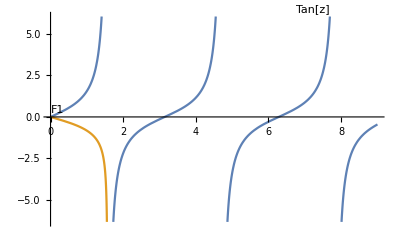

```mathematica
F1:= -1/(√(((π/2)/z)^2-1))
Plot[{Tan[z],F1},{z,0,9},PlotLabels-> Placed[{"Tan[z]","F1"},Above],GridLines->{{{π/2,{Red,Dashed}}},None}]
```

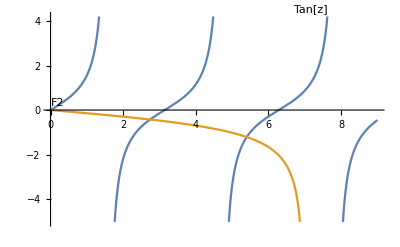

```mathematica
F2:= -1/(√((7/z)^2-1))
Plot[{Tan[z],F2},{z,0,9},PlotLabels-> Placed[{"Tan[z]","F2"},Above],GridLines->{{{π/2,{Thick,Red,Dashed}},{(3*π)/2,{Thick,Red,Dashed}},{(5*π)/2,{Thick,Red,Dashed}}},None}]
```

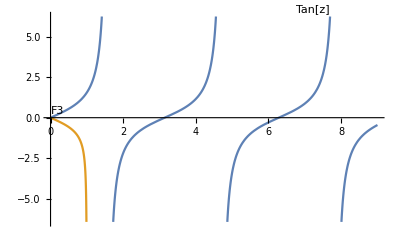

```mathematica
F3:= -1/(√((1/z)^2-1)) 
(* π/2 is aprrox 1.57 when Subscript[z, 0] < π/2 say 1. Then we will have no intersections. Because when z =π/2 we have an asymptote for Tan[z] and so does F3[z].*)
Plot[{Tan[z],F3},{z,0,9},PlotLabels-> Placed[{"Tan[z]","F3"},Above],GridLines->{{{π/2,{Thick,Red,Dashed}},{(3*π)/2,{Thick,Red,Dashed}},{(5*π)/2,{Thick,Red,Dashed}}},None}](* Clearly there are no intersections.*)
```

5)Problem 4.11)part a) We can the check the normalization constant value c_0 that we got for this problem based on  the value for n and l.

```mathematica
R20[r_]:= (Subscript[c, 0]/(2*a))*(1-(r/(2*a)))ⅇ^(-r/(2*a))
Assuming[a >0,Solve[Integrate[r^2*Abs[R20[r]]^2,{r,0,∞}]==1,Subscript[c, 0]]](*We have to take the positive root and the answer matches with the one computed manually.*)
```

{{c_0→-(√2)/(√a)},{c_0→(√2)/(√a)}}

```mathematica
R21[r_]:= (Subscript[c, 0]/(4*a^2))*(r)*(ⅇ^(-r/(2*a)))
Assuming[a >0,Solve[Integrate[r^2*Abs[R21[r]]^2,{r,0,∞}]==1,Subscript[c, 0]]](* Again we have to take the positive root and the answer matches with the one computed manually.*)
```

{{c_0→-(√(2/3))/(√a)},{c_0→(√(2/3))/(√a)}}